# Ejercicio 4.9

## Isaac Ayala A01184862

## Datos

```mathematica
motorData1200rpm={{0,5},{0.1,20},{0.2,40},{0.3,60},{0.4,79},{0.5,93},{0.6,102},{0.8,114},{1,120},{1.2,125}};
```

```mathematica
Ra=0.2;
Rfw=100;
Rfc={0,150};
Rf=Rfw+Rfc;
Vf=120;

Rab=0;
Vtb=120;
```

```mathematica
Vfmin=Table[{motorData1200rpm[[i,1]],motorData1200rpm[[i,1]]*Rf[[1]]},
{i,1,Length[motorData1200rpm]}];
Vfmax=Table[{motorData1200rpm[[i,1]],motorData1200rpm[[i,1]]*Rf[[2]]},
{i,1,Length[motorData1200rpm]}];
```

## Fórmulas

```mathematica
Vt=Rf*if;
(** Ea **) Varmadura=Vt+ia*Ra;
```

#### Generación de Splines - Obtención de la función de Ea.

```mathematica
a[j_]:=motorData1200rpm[[j+1,2]];
x[j_]:=motorData1200rpm[[j+1,1]];
h[j_]:=x[j+1]-x[j];
```

```mathematica
matrix2=Table[
Which[
i==j,h[i-1],
i==j-1,2(h[i-1]+h[i]),
i==j-2,h[i],
i≠ j||i≠j-1||i≠j-2,0
],
{i,Length[motorData1200rpm]-2},
{j,Length[motorData1200rpm]}];
```

```mathematica
res=Table[
3/h[j](a[j+1]-a[j])-3/h[j-1](a[j]-a[j-1]),
{j,Length[motorData1200rpm]-2}
];
```

```mathematica
sol=LinearSolve[matrix2,res] ;
```

```mathematica
c[j_]:=LinearSolve[matrix2,res] [[j+1]];
```

```mathematica
d[j_]:=1/(3h[j])(c[j+1]-c[j]);
```

```mathematica
b[j_]:=1/h[j](a[j+1]-a[j])-h[j]/3(2c[j]+c[j+1]);
```

```mathematica
Table[
{a[i]+b[i]*(y-x[i])+c[i]*(y-x[i])^2+d[i]*(y-x[i])^3,
x[i]≤y≤x[i+1]},
{i,0,Length[motorData1200rpm]-2}]
```

{{5+130.313 y+108.882 y^2+879.859 y^3,0≤y≤0.1},{20+178.485 (-0.1+y)+372.84 (-0.1+y)^2-1576.94 (-0.1+y)^3,0.1≤y≤0.2},{40+205.745 (-0.2+y)-100.243 (-0.2+y)^2+427.913 (-0.2+y)^3,0.2≤y≤0.3},{60+198.534 (-0.3+y)+28.1312 (-0.3+y)^2-1134.71 (-0.3+y)^3,0.3≤y≤0.4},{79+170.119 (-0.4+y)-312.282 (-0.4+y)^2+110.927 (-0.4+y)^3,0.4≤y≤0.5},{93+110.99 (-0.5+y)-279.004 (-0.5+y)^2+691.003 (-0.5+y)^3,0.5≤y≤0.6},{102+75.9197 (-0.6+y)-71.703 (-0.6+y)^2-39.477 (-0.6+y)^3,0.6≤y≤0.8},{114+42.5012 (-0.8+y)-95.3892 (-0.8+y)^2+164.415 (-0.8+y)^3,0.8≤y≤1},{120+24.0753 (-1+y)+3.25966 (-1+y)^2+6.8181 (-1+y)^3,1≤y≤1.2}}

```mathematica
Ea[y_]:=Piecewise[{{5+130.31316411090768 y+108.88249950239504 y^2+879.8585938852827 y^3,0≤y≤0.1},{20+178.4854218279452 (-0.1+y)+372.84007766797987 (-0.1+y)^2-1576.942959474319 (-0.1+y)^3,0.1≤y≤0.2},{40+205.74514857731162 (-0.2+y)-100.24281017431588 (-0.2+y)^2+427.9132440119979 (-0.2+y)^3,0.2≤y≤0.3},{60+198.53398386280844 (-0.3+y)+28.13116302928347 (-0.3+y)^2-1134.7100165736838 (-0.3+y)^3,0.3≤y≤0.4},{79+170.1189159714545 (-0.4+y)-312.2818419428218 (-0.4+y)^2+110.92682228276887 (-0.4+y)^3,0.4≤y≤0.5},{93+110.9903522513732 (-0.5+y)-279.00379525799116 (-0.5+y)^2+691.0027274425936 (-0.5+y)^3,0.5≤y≤0.6},{102+75.91967502305275 (-0.6+y)-71.70297702521312 (-0.6+y)^2-39.47699045025349 (-0.6+y)^3,0.6≤y≤0.8},{114+42.501245358937055 (-0.8+y)-95.38917129536522 (-0.8+y)^2+164.41472250339987 (-0.8+y)^3,0.8≤y≤1},{120+24.075343541198947 (-1+y)+3.2596622066746943 (-1+y)^2+6.818100436652966 (-1+y)^3,1≤y≤1.2}}];
```

## Desarrollo

Inciso a

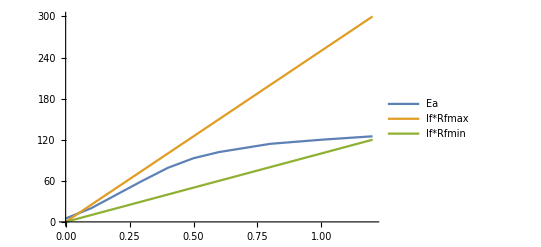

```mathematica
ListPlot[{motorData1200rpm,Vfmax,Vfmin},Joined->True,PlotLegends->{"Ea","If*Rfmax","If*Rfmin"}]
```

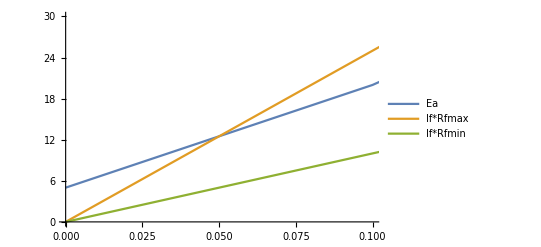

```mathematica
ListPlot[{motorData1200rpm,Vfmax,Vfmin},Joined->True,PlotLegends->{"Ea","If*Rfmax","If*Rfmin"},PlotRange->{{0,0.1},{0,30}}]
```

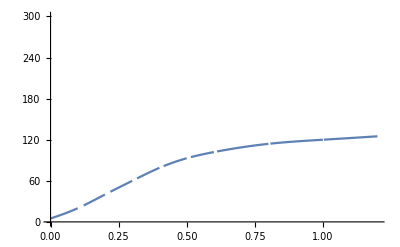

```mathematica
Plot[Ea[x],{x,0,1.2},PlotRange->{{0,1.2},{0,300}}]
```

Igualamos la función de Ea con las dos condiciones de Rf para obtener los valores de If.

```mathematica
Solve[Ea[y]-y*Rf[[1]]==0,y] (** Rf min **)
Solve[Ea[y]-y*Rf[[2]]==0,y] (** Rf max **)
```

{}

{{y→0.044186}}

Obersvamos que para Rf mínima, el valor está fuera del rango existente. De la gráfica asumimos un valor arbitrario de 1.25 ó 1.26 para If max.

```mathematica
if={1.26,0.04418604139618782}; (** if max, if min**)
```

Inciso b

Dado que no hay reacción de la armadura, Ra =0. Por lo tanto Vt = Ea. Obtenemos If.

```mathematica
NSolve[Ea[y]==120,y]
```

{{y→1.}}

Como Vt = If * (Rfw + Rfc), despejamos para Rfc

```mathematica
NSolve[Vtb==ifb*(Rfw+Rfcb),Rfcb]/.ifb->1
```

{{Rfcb→20.}}

## Resultados

Observamos una diferencia entre el resultado del libro y el resultado obtenido para el inciso a. Esto se debe a que la respuesta del solucionario se obtiene con métodos inexactos, aproximando solamente valores en una gráfica dibujada a mano. En este caso se obtuvo una función aproximada para Ea en base a los puntos dados. Con ello se resolvió la igualdad para cada situación de Rf.

```mathematica
Grid[
{
{"a)",""},
{"Vt max",if[[1]]*Rf[[1]]},
{"Vt min",if[[2]]*Rf[[2]]},
{"b)",""},
{"Rfc",NSolve[Vtb==ifb*(Rfw+Rfcb),Rfcb]/.ifb->1}
}
]
```

a) | 
Vt max | 126.
Vt min | 11.0465
b) | 
Rfc | {{Rfcb→20.}}